# De ecuaciones a código

## Matemáticas avanzadas (simbólicas y numéricas)

## Álgebra y Trigonometría

### Igualdades y desigualdades

Podemos utilizar dos signos igual == para verificar igualdad

```mathematica
Log[2,64]==6
```

True

```mathematica
Exp[ⅈ π]==1
```

False

```mathematica
Sin[x]/Cos[x]==Tan[x]
```

True

```mathematica
Sin[x]^2+Cos[x]^2==1
```

Cos[x]^2+Sin[x]^2==1

y también para representar ecuaciones.

```mathematica
1+z==15
```

Mathematica puede ser de mucha ayuda para resolver problemas de forma simbólica y numérica .

```mathematica
Solve[1+z==15,z]
```

{{z→14}}

```mathematica
Solve[{x^2+5==y,7 x-5==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

```mathematica
NSolve[360+234 x-1051 x^2+11 x^3+304 x^4-20 x^5==0,x]
```

{{x→-1.79025},{x→-0.498678},{x→0.797819},{x→1.68398},{x→15.0071}}

También es posible trabajar con desigualdades.

```mathematica
Reduce[{0<x<2,1<=x<=4},x]
```

1≤x<2

```mathematica
Reduce[Abs[3/(4x+1)]<=Abs[1/(x+1)],x,Reals]
```

x<-1||-1<x≤-4/7||x≥2

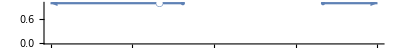

```mathematica
NumberLinePlot[x<-1||-1<x≤-4/7||x≥2,{x,-3,3}]
```

### Factorización, expansión y simplificación de expresiones

```mathematica
Factor[x^6-y^6+x^3 y^3-x^2 y^4+x y^5]
```

(x^2-x y+y^2) (x^4+x^3 y-y^4)

```mathematica
Expand[(x^2-x y+y^2) (x^4+x^3 y-y^4)]
```

x^6+x^3 y^3-x^2 y^4+x y^5-y^6

En cálculos algebraicos complicados resulta de gran ayuda simplificar expresiones.

```mathematica
Sqrt[1+Cos[x]]^2+Sqrt[1-Cos[x]]^2
```

2

```mathematica
expr=Sin[x]^4+2 Cos[x]^2 Sin[x]^2+Cos[x]^4
```

Cos[x]^4+2 Cos[x]^2 Sin[x]^2+Sin[x]^4

```mathematica
Simplify[expr]
```

1

```mathematica
Simplify[Sin[x]^2+Cos[x]^2==1]
```

True

```mathematica
Simplify[a^3+b^3+c^3-3 a b c,a+b+c==0]
```

0

```mathematica
Simplify[Sqrt[x^2+2 x+1],Assumptions->x∈Reals]
```

Abs[1+x]

Existe otra función para simplificación: FullSimplify, que realiza simplificaciones que involucran funciones especiales.

```mathematica
Simplify[BesselJ[n,x]+ⅈ BesselY[n,x]]
```

BesselJ[n,x]+ⅈ BesselY[n,x]

```mathematica
FullSimplify[BesselJ[n,x]+ⅈ BesselY[n,x]]
```

HankelH1[n,x]

### Expresiones trigonométricas

Existen funciones especiales para tratar de mejor manera las funciones trigonométricas.

```mathematica
TrigExpand[Sin[2 x]]
```

2 Cos[x] Sin[x]

```mathematica
TrigFactor[Cos[x]^2-Sin[x]^2]
```

2 Sin[π/4-x] Sin[π/4+x]

```mathematica
TrigReduce[2 Sin[x] Cos[y]]
```

Sin[x-y]+Sin[x+y]

```mathematica
TrigReduce[Sin[x]^2+Cos[x]^2]
```

1

## Cálculo

### Límites

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x->∞]
```

2/5

También podemos especificar la dirección de límite.

```mathematica
Limit[1/x,x->0,Direction->1]
```

-∞

```mathematica
Limit[1/x,x->0,Direction->-1]
```

∞

### Derivadas

```mathematica
D[x^6,x]
```

6 x^5

Con notación prima

```mathematica
Sin'[x]
```

Cos[x]

Definiendo la función previamente

```mathematica
f[x_]:=x^6+2 x+1;
f'[x]
```

2+6 x^5

Obtener derivadas de orden mayor

```mathematica
D[x^6+2 x+1,{x,6}]
```

720

### Integrales

Integrales indefinidas

```mathematica
Integrate[8 x^4,x]
```

(8 x^5)/5

```mathematica
(* Esc intt Esc *)
```

```mathematica
∫8 x^4 ⅆx
```

(8 x^5)/5

Integrales definidas

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

```mathematica
(* Esc dintt Esc *)
∫_0^π Sin[x]ⅆx
```

2

Obtener una aproximación numérica

```mathematica
NIntegrate[x^3 Sin[x]+2 Log[3 x]^2,{x,0,Pi}]
```

28.1531

### Secuencias, sumas y series

Podemos generar secuencias a partir de su función generadora.

```mathematica
Table[x^2,{x,1,7}]
```

{1,4,9,16,25,36,49}

Algunas secuencias conocidas ya vienen incorporadas

```mathematica
Table[Fibonacci[x],{x,1,7}]
```

Podemos hallar la función de generación para una secuencia

```mathematica
FindSequenceFunction[{2,4,6,8},n]
```

2 n

También podemos producir secuencias recursivas

```mathematica
RecurrenceTable[{a[x]==2 a[x-1],a[1]==1},a,{x,1,8}]
```

{1,2,4,8,16,32,64,128}

Calcular la suma de una secuencia a partir de su función generadora

```mathematica
Sum[i (i+1),{i,1,10}]
```

440

También podemos calcular sumas hasta infinito,

```mathematica
(* Esc sumt Esc *)
∑_(n=1)^∞ (-1)^(n+1)/n
```

Log[2]

```mathematica
∑_(n=1)^∞ n
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ n

indefinidas y múltiples.

```mathematica
∑_(i=1)^n ∑_(j=1)^n i j
```

1/4 n^2 (1+n)^2

Podemos generar aproximaciones de series de potencias para combinaciones de funciones incorporadas o indefinidas

```mathematica
Series[Exp[x^2],{x,0,8}]
```

1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9

```mathematica
Normal[%]
```

1+x^2+x^4/2+x^6/6+x^8/24

```mathematica
Series[2 f[x]-3,{x,0,3}]
```

-1+4 x+O[x]^4

```mathematica
ClearAll@f
(* ClearAll[f] hace lo mismo que la línea anterior *)
```

```mathematica
Series[2 f[x]-3,{x,0,3}]
```

(-3+2 f[0])+2 f'[0] x+f''[0] x^2+1/3 f^(3)[0] x^3+O[x]^4

### Cálculo multivariable

## Álgebra Lineal

### Vectores

```mathematica
u={1,2,3};
v={2,-1,0};
```

```mathematica
u+v
```

{3,1,3}

```mathematica
u-v
```

{-1,3,3}

```mathematica
Dot[u,v]
```

0

```mathematica
u.v
```

0

```mathematica
VectorAngle[u,v]
```

π/2

```mathematica
Cross[u,v]
```

{3,6,-5}

```mathematica
(* Esc cross Esc *)
u×v
```

{3,6,-5}

```mathematica
Norm[v]
```

√5

```mathematica
Projection[u,v]
```

{0,0,0}

```mathematica
Projection[u,{1,0,0}]
```

{1,0,0}

### Matrices

Construcción y visualización de matrices

```mathematica
mat1={{a,b}, {c,d}}
```

{{a,b},{c,d}}

```mathematica
MatrixForm[mat1]
```

(a | b
c | d)

```mathematica
MatrixQ[mat1]
```

True

```mathematica
MatrixQ[u]
```

False

```mathematica
mat2={{1,2}, {3,4}}
```

{{1,2},{3,4}}

```mathematica
MatrixForm[mat2]
```

(1 | 2
3 | 4)

```mathematica
IdentityMatrix[6]
```

{{1,0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,0,0,0,1}}

```mathematica
DiagonalMatrix[{6,7,7,6}]//MatrixForm
```

(6 | 0 | 0 | 0
0 | 7 | 0 | 0
0 | 0 | 7 | 0
0 | 0 | 0 | 6)

```mathematica
Table[If[i>=j,1,0],{i,4},{j,5}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 0)

Operaciones con matrices

```mathematica
mat1*mat2
```

{{a,2 b},{3 c,4 d}}

```mathematica
mat1.mat2//MatrixForm
```

(a+3 b | 2 a+4 b
c+3 d | 2 c+4 d)

```mathematica
mat3={{1},{2}}//MatrixForm
```

(1
2)

```mathematica
(mat4={{1},{2}})//MatrixForm
```

(1
2)

```mathematica
mat1.mat3
```

{{a,b},{c,d}}.(1
2)

```mathematica
mat1.mat4
```

{{a+2 b},{c+2 d}}

```mathematica
Inverse[{{1,1},{0,1}}]
```

{{1,-1},{0,1}}

```mathematica
Transpose[mat2]
```

{{1,3},{2,4}}

```mathematica
Det[mat1]
```

-b c+a d

```mathematica
Tr[{{1,2,3},{2,4,6},{4,8,9}}]
```

14

```mathematica
MatrixRank[{{1,2,3},{2,4,6},{4,8,9}}]
```

2

```mathematica
NullSpace[{{1,2,3},{2,4,6},{4,8,9}}]
```

{{-2,1,0}}

```mathematica
Eigensystem[{{1,2,3},{2,4,6},{4,8,9}}]
```

{{15,-1,0},{{3,6,10},{-1,-2,2},{-2,1,0}}}

Podemos resolveer el sistema m.x = b

```mathematica
LinearSolve[{{1,1},{0,1}},{x,y}]
```

{x-y,y}

```mathematica
PositiveDefiniteMatrixQ[{{1,1},{0,1}}]
```

True

```mathematica
SymmetricMatrixQ[{{1,1},{0,1}}]
```

False

```mathematica
OrthogonalMatrixQ[{{1,1},{0,1}}]
```

False

```mathematica
MatrixExp[{{1,1},{0,1}}]
```

{{ⅇ,ⅇ},{0,ⅇ}}

```mathematica
Exp[{{1,1},{0,1}}]
```

{{ⅇ,ⅇ},{1,ⅇ}}

```mathematica
MatrixPower[mat2,3]
```

{{37,54},{81,118}}

```mathematica
mat2^3
```

{{1,8},{27,64}}

```mathematica
KroneckerProduct[mat4,mat2]
```

{{1,2},{3,4},{2,4},{6,8}}

## Ecuaciones Diferenciales

```mathematica
DSolve[y'[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
DSolve[{y'[x]==y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^x}}

```mathematica
NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
```

{{y→InterpolatingFunction[…]}}

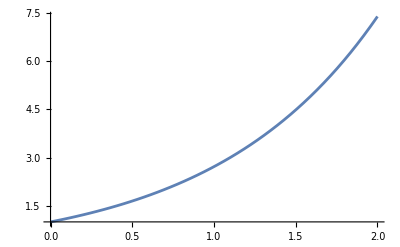

```mathematica
Plot[y[x]/. %,{x,0,2}]
```

```mathematica
DSolve[{x'[t]==-y[t],y'[t]==x[t]},{x[t],y[t]},t]
```

{{x[t]→C[1] Cos[t]-C[2] Sin[t],y[t]→C[2] Cos[t]+C[1] Sin[t]}}

```mathematica
DSolve[y'[x]==Piecewise[{{1,x<1},{0,x>=1}}],y[x],x]
```

{{y[x]→C[1]+(Piecewise[{{x, x≤1}, {1, True}}])}}

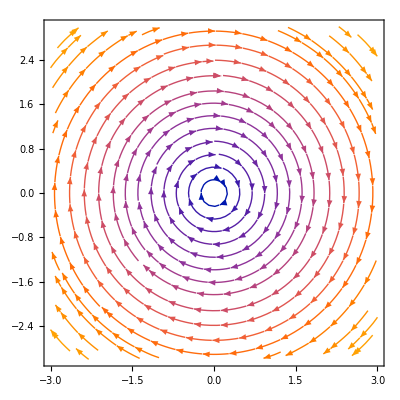

```mathematica
StreamPlot[{y,-x},{x,-3,3},{y,-3,3}]
```

```mathematica
LaplaceTransform[y'[t]+y[t]==1,y[t],s]
```

1/s^2+y'[t]/s==1/s

```mathematica
sol=Solve[s Y[s]-y0+Y[s]==1/s,Y[s]];
InverseLaplaceTransform[Y[s]/. sol[[1]],s,t]
```

1+ⅇ^-t (-1+y0)

```mathematica
FourierTransform[y'[t]+y[t]==1,y[t],s]
```

-ⅈ √(2 π) DiracDelta'[s]+√(2 π) DiracDelta[s] y'[t]==√(2 π) DiracDelta[s]

## Resumen de la clase

Mathematica puede ser de mucha ayuda para resolver problemas de forma simbólica y numérica.

Mathematica usa fracciones exactas y raíces exactas, no solo decimales.

Los vectores se representan mediante una lista de datos.

Las matrices se representan como una lista de listas, donde cada una de estas últimas representa las filas de la matriz.

Las matrices tienen implementadas funciones especiales para ser operadas.